## 134Ce - Petrache study

## The wobbling bands [8,10]

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* the YRAST band *)
band8En=Sort[N[#/1000]&@{7550,6776,5864,4761,4006,3207}];
band8Spins=Table[i,{i,10,20,2}];
(* the ONE-PHONON wobbling band *)
band10En=Sort[N[#/1000]&@{6523,5492,4697}];
band10Spins=Table[i,{i,13,17,2}];
```

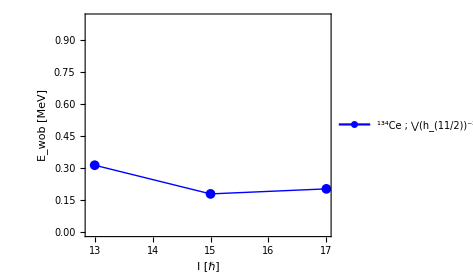

```mathematica
m1minipath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/Ce-Nucleus/134Ce-1.pdf";
wobbling[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i+1]]+yrast[[i+2]])},{i,1,Length[onephonon]}];
data=wobbling[band8En,band10En,band10Spins];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{Style[Row[{Superscript["","134"],"Ce ; ⋁(h_(11/2))^-2"}],FontFamily->"Arial",30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export[m1minipath,fig];
Show[fig]
```